## Execute this

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data=SortBy[Import["data/In_and_out_angles_PEG3percentBCR.xlsx"][[1,3;;]]/180,First];
```

```mathematica
numcoll=Length@data;
```

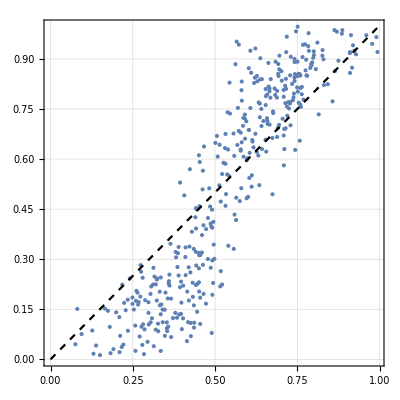

```mathematica
Show[{ListPlot[data,Frame->True,AspectRatio->1,GridLines->Automatic],Plot[x,{x,0,1},PlotStyle->{Black,Dashed}]}]
```

```mathematica
Needs["ErrorBarPlots`"]
dθ=0.1;
temp=Append[Table[FirstPosition[data[[;;,1]],_?(#>θ&)],{θ,0.0,1-dθ,dθ}]//Flatten,numcoll];
meanscatter=Table[Mean[data[[temp[[i]];;temp[[i+1]]]]],{i,1,Length@temp-1}];
varscatter=Table[Variance[data[[temp[[i]];;temp[[i+1]]]]],{i,1,Length@temp-1}];
meanscatterdatwiderror=Table[{meanscatter[[i]],ErrorBar[Sqrt@varscatter[[i,2]]]},{i,1,Length@meanscatter}];
```

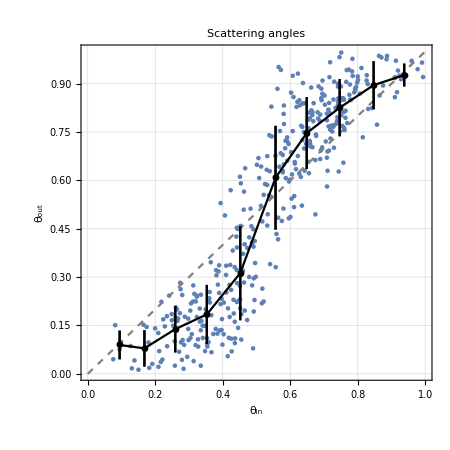

```mathematica
Show[{ListPlot[data,PlotRange->{{0,1},{Automatic,1}},AspectRatio->1,Frame->True,GridLines->Automatic],Plot[x,{x,0,1},PlotStyle->{Gray,Dashed}],ErrorListPlot[meanscatterdatwiderror,PlotStyle->Black,Joined->True,PlotMarkers->Automatic]},PlotLabel->Style["Scattering angles",14], FrameLabel->{Style["θ_in",14],Style["θ_out",14]},ImageSize->450]
```

```mathematica
meanreorientation=Mean@Abs@Flatten@Differences@Transpose@data*180
```

22.8502

```mathematica
Mean@Flatten@Abs@Differences@Transpose@meanscatter*180
```

14.5938

```mathematica
varianceorientation=180*Sqrt@Variance@Abs@Flatten@Differences@Transpose@data
```

15.6134